# Beam splitters and interferometry

## Quantum mechanics of Beam splitters

Classically a lossless beam-splitter can be described as a device with one input mode and two output modes , related to transmitted and reflected amplitudes. However, this description is not adequate in a fully quantum approach because the commutation relations do not hold  [a_i ,a_j^†] = δ_ij,  [a_i , a_j] = 0 ,  [a_i^†,a_j^†] = 0.
A quantum description uses an extra mode that is  unused in the classical setup,  but in the quantum approach it can have a quantized field in the vacuum state that has relevant physical effects . Using this description the commutation relations hold and we can analyze behaviors that can not be explained classically.

```mathematica
QuantumCircuitOperator[{"XSpider"["BS"]->{2,1}->{2,1}}]["Diagram","WireLabels"->{1->{Placed["(â)_0",Left],Placed["(â)_2",Right]},2->{Placed["(â)_1",Left],Placed["(â)_3",Right]}},FontSize->18]
```

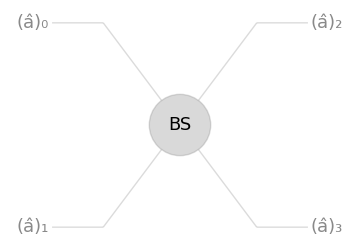
```mathematica
-Graphics--Graphics-
```

The beam splitter can be described as a device with 2 input modes and 2 output modes. The field creation operators can be related between input and output modes using  the complex reflectance and transmittance coefficients

## Properties of quantum beam-splitters

```mathematica
setFockSize[40]
```

```mathematica
a2 = QuantumTensorProduct[a,QuantumOperator["I"[fockBasis["Dimension"]]]];
a3 = QuantumTensorProduct[QuantumOperator["I"[fockBasis["Dimension"]]],a];
```

Using the relations between r,t and r', t' and considering a phase shift of ± ⅈ between reflected and transmitted beams we can get the matrix:
BS(r, t) = (r | ⅈ t
ⅈ t | r)

```mathematica
BSMatrixEvolve[r_,t_]:= {{r,ⅈ t},{ⅈ t,r}} /; Abs[r]^2+Abs[t]^2 == 1
```

Expressing the a_(0,)a_1 operators in terms of a_2,a_3

```mathematica
{a0,a1} = Inverse[BSMatrixEvolve[1/√2, 1/√2]].{a2,a3};
```

```mathematica
a1["Dagger"][];
```

(|0⟩)_0(|1⟩)_1 ⇒^BS   1/√2((|0⟩)_2(|1⟩)_3 + ⅈ(|1⟩)_2(|0⟩)_3 )

```mathematica
%["Formula"]
```

1/(√2)01+ⅈ/(√2)10

The output state results in  a entangled state:

```mathematica
QuantumEntanglementMonotone[%%,{1,2}]
```

1

If we put one photon in each of the input ports the two photons emerge together (explained by interference when the photons are indistinguishable)
 (|1⟩)_0(|1⟩)_1 ⇒^BS   ⅈ/√2((|2⟩)_2(|0⟩)_3 + (|0⟩)_2(|2⟩)_3 )

```mathematica
a1["Dagger"]@a0["Dagger"][]
```

ⅈ/(√2)02+ⅈ/(√2)20

Now let’s try using a coherent state in the input port one (|0⟩)_0(|α⟩)_1 , using OverHat[D_1](α) = exp(α a_1^†-α*a_1)

```mathematica
disp[α_?NumericQ,creation_QuantumOperator]:= Exp[α N[creation]["Dagger"]-α*N[creation]]
```

```mathematica
αcoh = RandomReal[{0,3}]Exp[I RandomReal[{0,2Pi}]]
```

1.53155-0.584302 ⅈ

```mathematica
(* cohBS = disp[αcoh, a1][]  too slow *)
```

```mathematica
RepeatedTiming[cohBS =QuantumState[MatrixExp[(αcoh a1["Dagger"]-αcoh* a1)["Matrix"],PadRight[{1},fockBasis["Dimension"]^2]],a1["OutputDimensions"]] ]
```

{0.181816,QuantumState[…]}

Really close to zero , so it is a product state (not entangled)

```mathematica
QuantumEntanglementMonotone[cohBS,{{1},{2}}]
```

2.03836×10^-9

The theoretical result represents that a coherent state resembles a classical field that divides evenly in a 50:50 BS (average photon number |α|^2/2 in each output mode and phase shift π/2 for the reflected wave):
(|0⟩)_0(|α⟩)_1 ⇒^BS   ((|(ⅈ α)/(√2)⟩)_2 (|α/(√2)⟩)_3 )

Comparing the states:

```mathematica
(cohBS - QuantumTensorProduct[coh[ⅈ αcoh/√2],coh[αcoh/√2]])//Chop
```

0

Also the beam splitter causes the transformation that the N photons are binomially distributed over the two modes
(|0⟩)_0(|N⟩)_1 ⇒^BS  1/2^(N/2) ∑_(n=0)^N [(N!)/(n! (N-n)!)]^(1/2)((|n ⟩)_2|N-n ⟩)_3

```mathematica
Np = 8;
```

```mathematica
(* (a1^Np)["Dagger"] too slow *)
```

```mathematica
(QuantumState[MatrixPower[a1["Dagger"]["Matrix"],Np,PadRight[{1},fockBasis["Dimension"]^2]],a1["OutputDimensions"]]//Simplify )["Normalize"]//RepeatedTiming
```

{0.036973,1/16 08+ⅈ/(4 √2)17-(√7)/826-1/4 ⅈ √(7/2)35+(√(35/2))/8 44+1/4 ⅈ √(7/2)53-(√7)/862-ⅈ/(4 √2)71+1/16 80}

```mathematica
Table[1/2^(Np/2)ⅈ^n √((Np!)/(n!(Np-n)!)),{n,0,Np}]
```

{1/16,ⅈ/(4 √2),-(√7)/8,-1/4 ⅈ √(7/2),(√(35/2))/8,1/4 ⅈ √(7/2),-(√7)/8,-ⅈ/(4 √2),1/16}

```mathematica
%%[[2]]["AmplitudeList"] == %
```

True

## Single photon Mach-Zehnder Interferometer (Unbalanced BS)

What is the probability of finding a photon in output mode 5?

```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
setFockSize[5]
```

```mathematica
a1 = QuantumTensorProduct[a,QuantumOperator["I"[fockBasis["Dimension"]]]];
a2 = QuantumTensorProduct[QuantumOperator["I"[fockBasis["Dimension"]]],a];
```

```mathematica
a1@a2["Dagger"]-a2["Dagger"]@a1
```

0

There is also other type of BS that has a phase shift of π of the reflected wave and has the following matrix:

```mathematica
BSMatrixEvolve2[r_,t_]:= {{r,t},{t,-r}} /; Abs[r]^2+Abs[t]^2 == 1
```

```mathematica
Clear[a1,a2]
```

```mathematica
a5 = QuantumTensorProduct[a,QuantumOperator["I"[fockBasis["Dimension"]]]];
a6 = QuantumTensorProduct[QuantumOperator["I"[fockBasis["Dimension"]]],a];
```

```mathematica
backEvolve = BSMatrixEvolve2[1/√2,1/√2] . QuantumOperator["P"[ϕ]]["Matrix"]. BSMatrixEvolve2[√(4/5),√(1/5)] //Inverse //Simplify
```

{{(2+ⅇ^(-ⅈ ϕ))/(√10),(2-ⅇ^(-ⅈ ϕ))/(√10)},{(ⅇ^(-ⅈ ϕ) (-2+ⅇ^(ⅈ ϕ)))/(√10),(1+2 ⅇ^(-ⅈ ϕ))/(√10)}}

Relating the final and initial operators (Heisenberg like evolution):

```mathematica
{a1,a2} = backEvolve.{a5,a6}
```

{QuantumOperator[…],QuantumOperator[…]}

```mathematica
(a1["Dagger"]@QuantumState["00",fockBasis])["Probability"]
```

<|01→(Abs[2-ⅇ^(ⅈ Conjugate[ϕ])]^2)/(10 (1/10 Abs[2-ⅇ^(ⅈ Conjugate[ϕ])]^2+1/10 Abs[2+ⅇ^(ⅈ Conjugate[ϕ])]^2)),10→(Abs[2+ⅇ^(ⅈ Conjugate[ϕ])]^2)/(10 (1/10 Abs[2-ⅇ^(ⅈ Conjugate[ϕ])]^2+1/10 Abs[2+ⅇ^(ⅈ Conjugate[ϕ])]^2))|>

```mathematica
FullSimplify[%//Values,Element[ϕ,Reals]]//ComplexExpand //TrigReduce
```

{1/10 (5-4 Cos[ϕ]),1/10 (5+4 Cos[ϕ])}

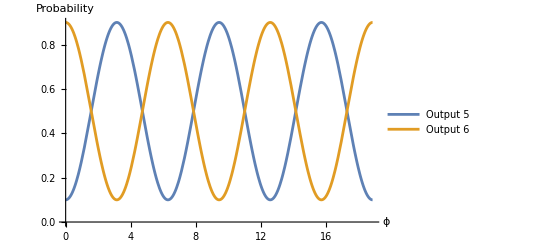

```mathematica
Plot[%,{ϕ,0,6Pi},AxesLabel->{"ϕ","Probability"},PlotLegends->{"Output 5","Output 6"}]
```

## Interference of coherent states

Let’s analyze interferometry of coherent states in a Mach Zehnder interferometer, we should expect similar results than using classical light. Calling ĉ and d̂ the final output modes after the second BS:

```mathematica
setFockSize[40]
```

```mathematica
c = QuantumTensorProduct[a,QuantumOperator["I"[fockBasis["Dimension"]]]];
d = QuantumTensorProduct[QuantumOperator["I"[fockBasis["Dimension"]]],a];
```

```mathematica
θ = RandomReal[{0,2Pi}];
```

The MZI can be describe as  BS evolution, a path difference and a second BS evolution

```mathematica
backevolveMZI[θ1_] := Inverse[BSMatrixEvolve[1/√2, 1/√2].DiagonalMatrix[{ⅇ^(ⅈ θ1),1}]. BSMatrixEvolve[1/√2, 1/√2]]//Simplify
```

Relating the operators:

```mathematica
{a0,a1} = backevolveMZI[θ].{c,d};
```

```mathematica
outstate =QuantumState[MatrixExp[(αcoh a1["Dagger"]-αcoh* a1)["Matrix"],PadRight[{1},fockBasis["Dimension"]^2]],a1["OutputDimensions"]]
```

QuantumState[…]

```mathematica
QuantumEntanglementMonotone[outstate,{{1},{2}}]
```

4.03725×10^-10

The expression that relates the evolution of the coherent state in port 1 is:
(|0⟩)_0(|α⟩)_1⇒^BS(|ⅈ ((ⅇ^(ⅈ θ)+1) α)/2⟩)_c(|((1- ⅇ^(ⅈ θ)) α)/2⟩)_d

```mathematica
(outstate -QuantumTensorProduct[coh[(ⅈ (ⅇ^(ⅈ θ)+1)αcoh)/2],coh[((1-ⅇ^(ⅈ θ))αcoh)/2]])//Chop
```

0

Phase shift θ can be measured subtracting the intensities from two detectors D_1 and D_2. That can be represented by ⟨Ô ⟩ with  Ô = c^†c-d^†d the number difference operator. This is simple to calculate because the mean of the number operator on a coherent state is just the magnitude of the complex squared.

```mathematica
Clear[θ]
```

```mathematica
Ocurrent = c["Dagger"]@c -d["Dagger"]@d;
```

```mathematica
OmeanSymbolic = FullSimplify[Abs[(ⅈ (ⅇ^(ⅈ θ)+1)α)/2]^2-Abs[((1-ⅇ^(ⅈ θ))α)/2]^2,Element[θ,Reals]]
```

α Conjugate[α] Cos[θ]

```mathematica
OmeanNumeric =Table[a1 = (backevolveMZI[θ].{c,d})[[2]];outstate =QuantumState[MatrixExp[(αcoh a1["Dagger"]-αcoh* a1)["Matrix"],PadRight[{1},fockBasis["Dimension"]^2]],a1["OutputDimensions"]] ;
(outstate["Dagger"]@ Ocurrent @ outstate)["Scalar"]//Chop,{θ,N @ Subdivide[0,2Pi,39]}]
```

{2.68707,2.65227,2.54878,2.37928,2.14816,1.8614,1.52643,1.15193,0.74759,0.32389,-0.108197,-0.537483,-0.952848,-1.34353,-1.69942,-2.0113,-2.27108,-2.47205,-2.60899,-2.67836,-2.67836,-2.60899,-2.47205,-2.27108,-2.0113,-1.69942,-1.34353,-0.952848,-0.537483,-0.108197,0.32389,0.74759,1.15193,1.52643,1.8614,2.14816,2.37928,2.54878,2.65227,2.68707}

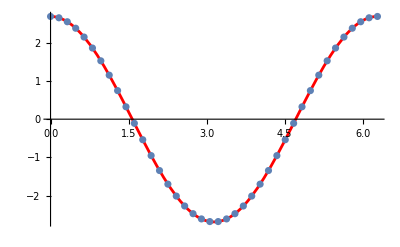

```mathematica
Show[Plot[OmeanSymbolic/.α->αcoh,{θ,0,2Pi},PlotStyle->Red],ListPlot[Thread[{N @ Subdivide[0,2Pi,39],OmeanNumeric}]]]
```

We observe the result analogous to classical coherent light, but coherent states are still quantum states and possess quantum mechanical fluctuations. Using error propagation the uncertainty  of phase measurement is Δθ = ΔO/ |(ⅆ ⟨O⟩)/ⅆθ| = 1/(√(n^—)|sin(θ)| ), which is optimal or minimum for odd multiples of π/2. That is the best result with classical-like states determining a standard quantum limit.